First for spin up:

```mathematica
sol=Assuming[Ef>0&&Js>0&&Δ>0,Solve[Ef==Js k^2+ 3√3/16 Δ k^4,k]//Simplify];
selectsol=4;
sol[[selectsol]]//Simplify
sol[[selectsol]]/.{Js->1,Ef->0.2,Δ->0.2}
Assuming[Ef>0&&hbar>0&&Δ>0&&m>0,sol/.{Js->hbar^2/(2m)}//Simplify][[2]]
slope=2 Js k +Δ( D[kx^3 kz,kx](√3)/2+D[kx^3 kz,kz] 1/2)/.{kx->k (√3)/2,kz->k 1/2}
slopesol=Assuming[Js>0&&Ef>0,Solve[(slope/.sol[[selectsol]])==0,Δ]]//Simplify
Simplify[(slope/.sol[[selectsol]])/.slopesol]
slopeup=Assuming[Js>0&&Ef>0&&0<γ<1,Simplify[(slope/.sol[[selectsol]]/.Δ->γ Δ)/.slopesol[[1]]]]
slopeup/.{Js->1,Ef->0.2,Δ->0.2,γ->1}
```

{k→(2 √((-2 Js+√(4 Js^2+3 √3 Ef Δ))/Δ))/3^(3/4)}

{k→0.444373}

{k→(2 ⅈ √((hbar^2+√(hbar^4+3 √3 Ef m^2 Δ))/(m Δ)))/3^(3/4)}

2 Js k+3/4 √3 k^3 Δ

{{Δ→-(4 Js^2)/(3 √3 Ef)}}

{0}

2 √2 √((Ef Js (-1+√(1-γ)) (-1+γ))/γ)

0.

and now for spin down:

```mathematica
sol=Assuming[Ef>0&&Js>0&&Δ>0,Solve[Ef==Js k^2- 3√3/16 Δ k^4,k]//Simplify];
selectsol=4;
sol[[selectsol]]//Simplify
sol[[selectsol]]/.{Js->1,Ef->0.2,Δ->0.2}
slope=2 Js k -Δ( D[kx^3 kz,kx](√3)/2-D[kx^3 kz,kz] 1/2)/.{kx->k (√3)/2,kz->k 1/2}
(*here we flip Δ, because the above solution assumes an opposite spin*)
Assuming[Js>0&&Ef>0,Simplify[(slope/.sol[[selectsol]]/.Δ->-Δ)/.slopesol]]
slopedown=Assuming[Js>0&&Ef>0&&0<γ<1,Simplify[(slope/.sol[[selectsol]]/.Δ->-γ Δ)/.slopesol[[1]]]]
slopedown/.{Js->1,Ef->0.2,Δ->0.2,γ->1}
```

{k→(2 √((2 Js+√(4 Js^2-3 √3 Ef Δ))/Δ))/3^(3/4)}

{k→3.89786}

2 Js k-3/8 √3 k^3 Δ

{√2 √(Ef Js)}

√2 (Js-Js √(1-γ)) √((Ef (1+√(1-γ)))/(Js γ))

0.632456

(√2 (Js (-1+√(1-γ)) √((Ef (1+√(1-γ)))/(Js γ))+2 √((Ef Js (-1+√(1-γ)) (-1+γ))/γ)))/(√(Ef Js))

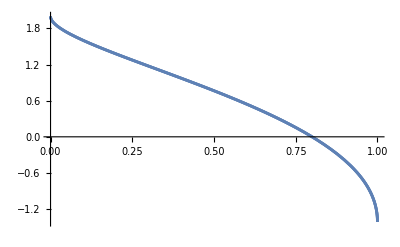

```mathematica
Assuming[Js>0&&Ef>0&&0<γ<1,Simplify[(slopeup-slopedown)/(√(Ef Js))]]
Plot[%/.{Js->{0.5,0.8,1.5},Ef->0.2,Δ->0.2},{γ,0,1}]
```

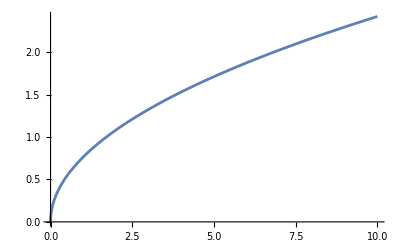

```mathematica
Plot[(slopeup-slopedown)/.{γ->0.5,Ef->1},{Js,0,10}]
```